# Лабораторная работа 2. Модель развития популяции. Модель Мальтуса

### Построим модель, где будет учитываться зависимость рождаемости и смертности от возраста.

## Заданные функции

### Функция начального распределения популяции

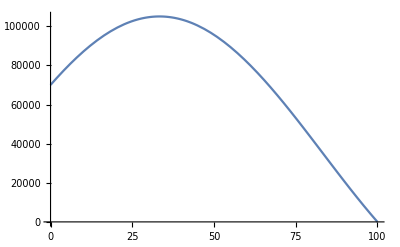

7.3593×10^6

```mathematica
f[a_]:=70000(1/2+Cos[π(a/100-1/3)])
Plot[f[a],{a,0,100}]
∫_0^100 f[a]ⅆa//N
```

```mathematica
f[a_]:=70000(1/2+Cos[π(a/100-1/3)+k])
Plot[f[a],{a,0,100}]
∫_0^100 f[a]ⅆa//N
```

-Graphics-

1.11408×10^6 (3.14159+3.4641 Cos[k]-2. Sin[k])

### Функция смертности

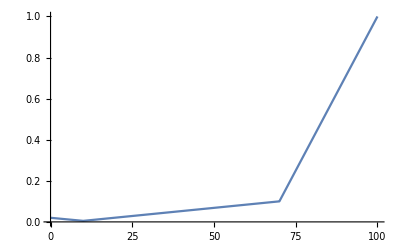

0.19775

```mathematica
μ[a_]:=Which[0≤a<10,1/50-(3 a)/2000,10≤a<70,-13/1200+(19 a)/12000,70≤a<100,-2+(3 a)/100,True,1]
Plot[μ[a],{a,0,100}]
(∫_0^100 μ[a]ⅆa)/100//N
```

### Функция рождаемости

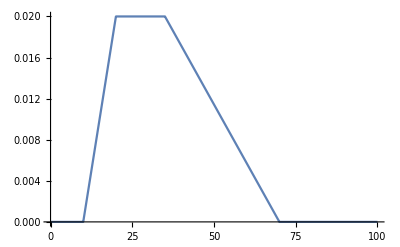

0.75

```mathematica
b[a_]:=Which[10≤a<20,-1/50+a/500,20≤a<35,2/100,35≤a<70,1/25-a/1750,True,0]
Plot[b[a],{a,0,100}]
∫_0^100 b[a]ⅆa//N
```

```mathematica
ClearAll[s]
```

```mathematica
g[t_]:=∫_0^100 b[s]f[s]ⅆs

(* Функции b и f должны быть связаны условием f(0) = g(0): *)
f[0]
g[0]//N
```

70000 (1/2+Sin[k+π/6])

126.651 (207.262+277.128 Cos[0.471239-k]-560. Cos[0.314159+k]+282.872 Cos[0.628319+k]+160. Sin[0.471239-k]-969.948 Sin[0.314159+k]+1129.95 Sin[0.628319+k])

```mathematica
Solve[N[f[0]]==N[g[0]],k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-2.79897},{k→0.0696145}}

```mathematica
k=0.06961449150267089;
```

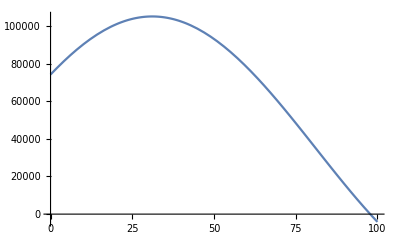

7.19497×10^6

```mathematica
f[a_]:=70000(1/2+Cos[π(a/100-1/3)+k])
Plot[f[a],{a,0,100}]
∫_0^100 f[a]ⅆa//N
```

```mathematica
g[t_]:=∫_0^100 b[s]f[s]ⅆs

(* Функции b и f должны быть связаны условием f(0) = g(0): *)
f[0]
g[0]//N
```

74132.

74132.

## 1. Получить математическую модель n[t,a]

n[t,a] - количество людей в момент времени t в возрасте a
N[t,a] - общая численность в t

Количество людей в возрасте а в момент времени Δt будет определяться разностью между количеством людей в возрасте a-Δt в момент времени t и количеством людей, которые умерли за Δt, т.е:

n(t+Δt,a)=n(t,a-Δt)-μ(a-δΔt)*n(t+δΔt,a-δΔt)*Δt, где δ [0,1].

Перейдем к пределу при Δt→0 и получим квазилинейное неоднородное дифференциальное уравнение в частных производных первого порядка. Решать его будем, решая систему ОДУ.
(∂n(t,a))/(∂t)+(∂n(t,a))/(∂a)=-μ(a)*n(t,a)(Von Foerster)

Добавим граничные условия:
n(0,a)=f(a) - количество людей возраста a;
n(t,0)=∫_0^∞ b(a)*n(t,a)ⅆa - количество рождаемых детей в момент времени t у людей возраста a.

Воспользуемся методом характеристик, чтобы найти решение данного уравнения (Von Foerster):
ⅆt/1+ⅆa/1=(ⅆn(t,a))/(-μ(a)n(t,a))
Piecewise[{{ⅆt/ⅆa=1, }, {ⅆn/-μn=ⅆt, }}]
Решением  этой системы будут два независимых интеграла Ф(I_1,I_2):
I_1=t-a;
       I_2=(n(t,a))/e^(-∫μ(a)ⅆa).
Ф(t-a,(n(t,a))/e^(-∫μ(a)ⅆa))
Неявное общее решение ДУ в частных производных
n(t,a)=ϕ(t-a)e^(-∫μⅆa)

Получаем прямые 
Piecewise[{{a=t+a_0,a>t, }, {a=t-t_0,a<t, }}]

Для a>t: n(t,a)=f(a-t)e^(-∫_(a-t)^a μ(s)ⅆs)
Для a<t: n(t,a)=n(t-a,0)e^(-∫_0^a μ(s)ⅆs)

Воспользуемся этими уравнениями и заданным ранее n(t,0)=∫_0^∞ b(a)*n(t,a)ⅆa , чтобы получить линейное уравнение 
n(t,0)=∫_0^t b(a)*n(t-a,0)e^(-∫_0^a  μ(s)ⅆs)ⅆa+∫_t^∞ b(a)*f(a-t)e^(-∫_(a-t)^a  μ(s)ⅆs)ⅆa.
Приближенно можно получить, что 
n(t,0)=∫_0^t b(a)*n(t-a,0)e^(-∫_0^a  μ(s)ⅆs)ⅆa,t→∞
Тогда n(t,a) можно выразить как  n(t,a)=n(t-a,0)e^(-∫_0^a  μ(s)ⅆs)

## 2. Построить график N(A) = ∫_0^∞ n[t,a]ⅆa a) t [0,10] b) t [0,100]

Будем искать решение через конечную сумму.
Воспользуемся всеми определенными ранее условиями.

Разобъем отрезок интегрирования

```mathematica
delta=1/12;
```

```mathematica
start=0;
end=100;
part=Range[start,end,delta];
```

```mathematica
n=Length[part];
```

```mathematica
ClearAll[NN]
```

```mathematica
NN[0,a_]:=f[a]
```

Определение значения при a=0,t=0

```mathematica
NN[0,0]:=f[0]
```

```mathematica
NN[t_,0]:=∑_(i=2)^n N[b[part⟦i⟧]NN[t,part⟦i⟧]delta]
NN[t_,a_]:=If[(aa=N[NN[t-delta,a-delta]-μ[a]NN[t-delta,a-delta]delta])>0,aa,0]
```

```mathematica
epochs=Table[{a,N[NN[t,a]]},{t,0,100},{a,0,100}];
```

$Aborted

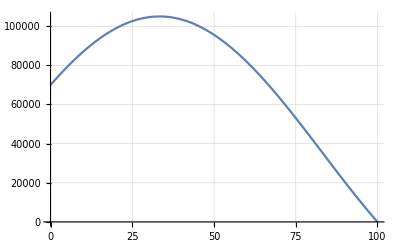
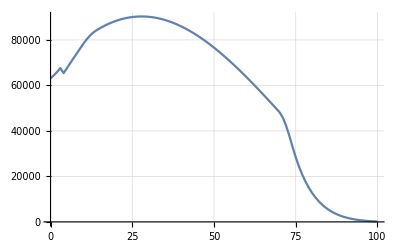
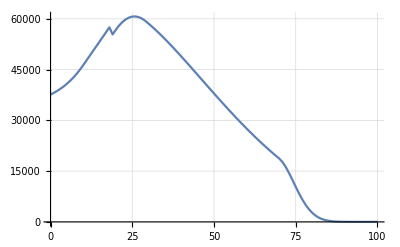
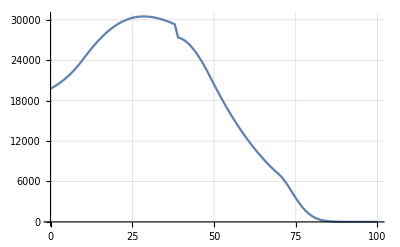
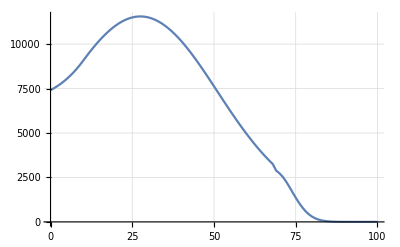
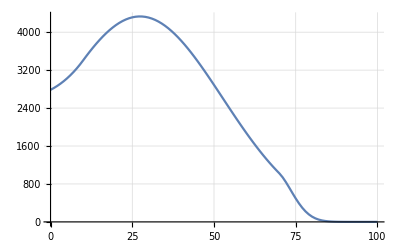

```mathematica
ListLinePlot[epochs⟦#,;;⟧,PlotRange->All,GridLines->Automatic]&/@listt
```

```mathematica
epochs10=Table[{a,N[NN[t,a]]},{t,0,10},{a,0,100}];
```

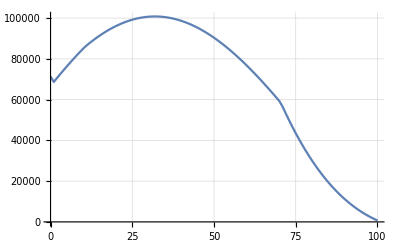
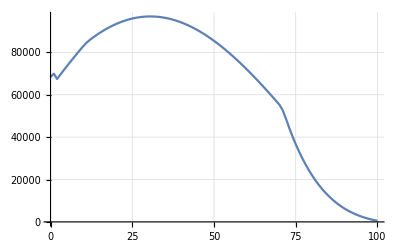
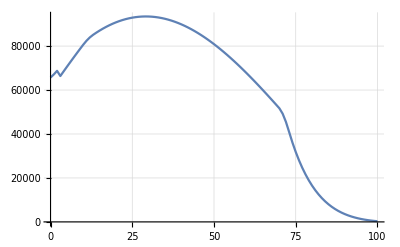
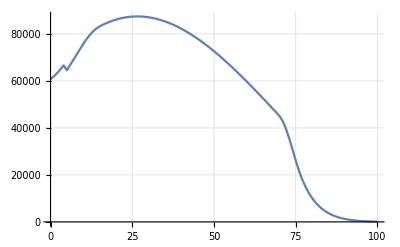
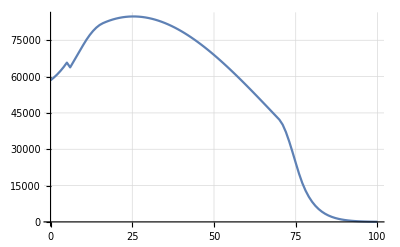
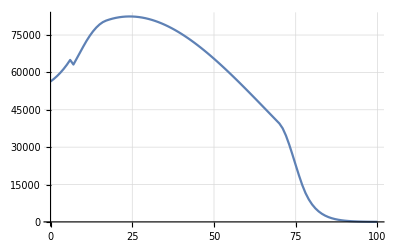
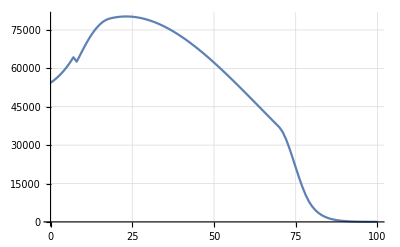
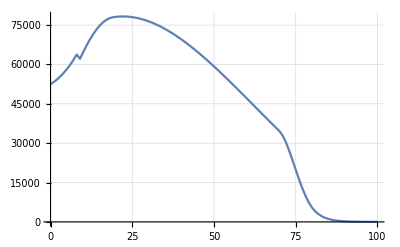
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[epochs10⟦#,;;⟧,PlotRange->All,GridLines->Automatic]&/@Range[10]
```

## 3. Сравнить с моделью Мальтуса f^(a),b^(a),μ - известные функции

Пусть в популяции с начальной численностью N особей за промежуток времени dt появляется dN новых особей. Если число вновь появившихся особей прямо пропорционально N и dt, то имеем уравнение dN=r*dt*N. 

Разделив обе части на dt получим 
dN/dt = r*N ,
где dN/dt - абсолютная скорость роста численности , r - биотический потенциал
решением уравнения будет

N(t)=N_0*e^kt , где k = b-μ
Тогда модель Мальтуса представима в виде:

N(t)=N_0*e^((b-μ)t)

```mathematica
Malthus[t_,a_]:=f [a]Exp[(b[a]-μ[a])t]
```

```mathematica
malthepoch=Table[{a,N[Malthus[t,a]]},{t,0,100},{a,0,100}];
```

```mathematica
listt={1,5,20,40,70,100};
```

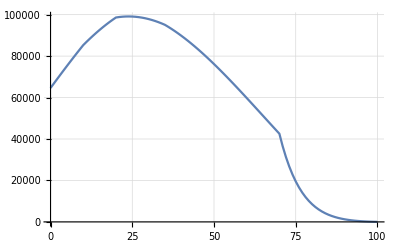
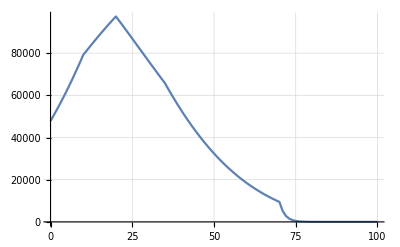
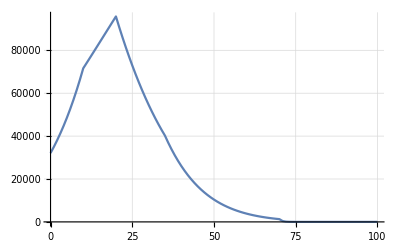
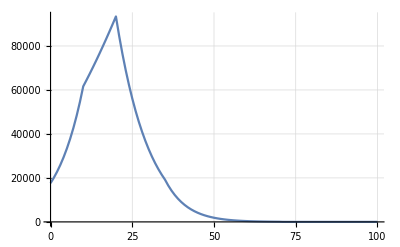
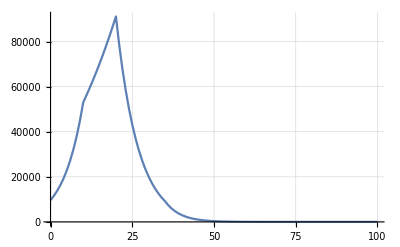
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[malthepoch⟦#,;;⟧,PlotRange->All,GridLines->Automatic]&/@listt
```

Модель Мальтуса и построенная нами модель

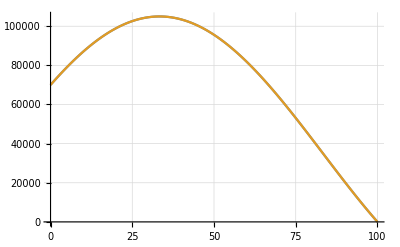
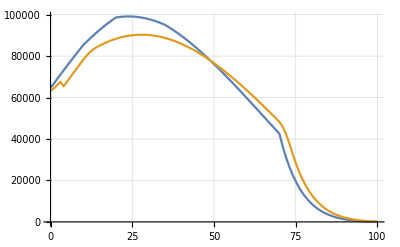
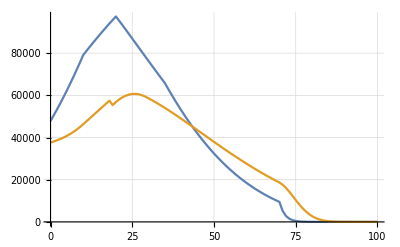
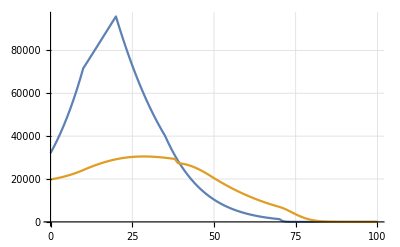
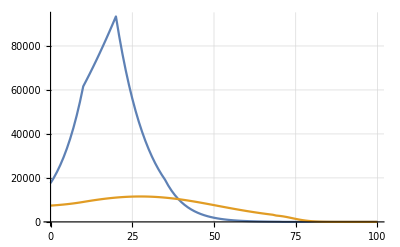
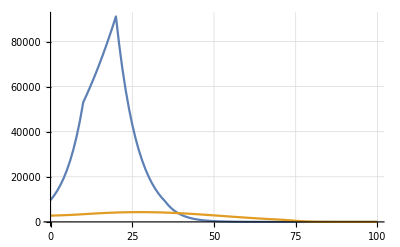

```mathematica
ListLinePlot[{malthepoch⟦#,;;⟧,epochs⟦#,;;⟧},PlotRange->All,GridLines->Automatic]&/@listt
```

Изменение  популяции со временем

```mathematica
epochs[[;;,;;,-1]]
```

{{70000.,71886.9,73737.4,75549.7,77321.9,91,7873.91,5860.34,3875.54,1921.45,0.},99,{1}}
 |  |  |  |

```mathematica
epochs[[1]][[;;,-1]]
```

{70000.,71886.9,73737.4,75549.7,77321.9,79052.4,80739.4,82381.3,83976.4,85523.2,87020.1,88465.7,89858.5,91197.2,92480.4,93706.9,94875.5,95985.,97034.3,98022.3,98948.2,99810.9,100610.,101344.,102012.,102615.,103151.,103619.,104020.,104352.,104617.,104812.,104939.,104996.,104985.,104904.,104755.,104536.,104249.,103894.,103470.,102979.,102421.,101797.,101106.,100351.,99530.4,98646.5,97699.8,96691.2,95621.8,94492.5,93304.5,92058.9,90757.1,89400.2,87989.7,86526.8,85013.1,83450.,81839.1,80182.,78480.3,76735.7,74949.9,73124.7,71261.9,69363.3,67430.7,65466.2,63471.6,61448.9,59400.,57327.2,55232.2,53117.3,50984.6,48836.,46673.8,44500.1,42317.,40126.7,37931.3,35733.,33534.,31336.5,29142.6,26954.4,24774.2,22604.1,20446.2,18302.7,16175.6,14067.1,11979.3,9914.24,7873.91,5860.34,3875.54,1921.45,0.}

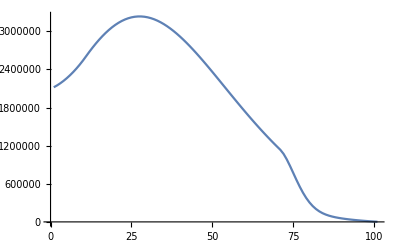

```mathematica
model=ListLinePlot[Total[epochs[[;;,;;,-1]]],PlotRange->All]
```

```mathematica
malthepoch
```

{{{0,70000.},{1,71886.9},{2,73737.4},{3,75549.7},93,{97,5860.34},{98,3875.54},{99,1921.45},{100,0.}},99,{1}}
 |  |  |  |

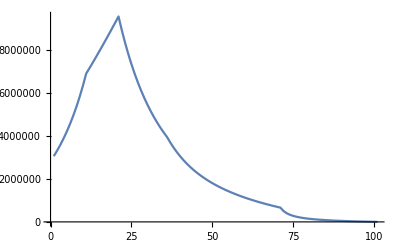

```mathematica
malthusmodel=ListLinePlot[Total[malthepoch[[;;,;;,-1]]],PlotRange->All]
```

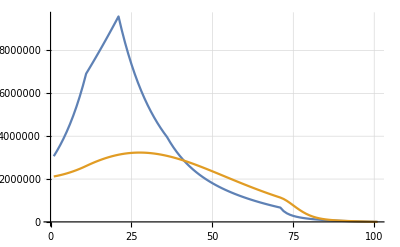

```mathematica
ListLinePlot[{Total[malthepoch[[;;,;;,-1]]],Total[epochs[[;;,;;,-1]]]},PlotRange->All,GridLines->Automatic]
```